```mathematica
Subscript[ψ, i_][ξ_]:=Subscript[ψ, i][ξ]=LegendreP[i,x]/.{x->ξ}
Subscript[Φ, i_][ξ_]:=Subscript[Φ, i][ξ]=√(2/(∫_-1^1 (Subscript[ψ, i][x])^2 ⅆx))*Subscript[ψ, i][ξ]
maxPolynomialOrder = 20;
legendreTable = Table[Subscript[Φ, i][x],{i,0,maxPolynomialOrder}];
Subscript[ϕ, i_][ξ_]:=legendreTable[[i+1]]/.{x->ξ}
cellCenter[j_,Δx_, xLeft_]:=(xLeft + (j-1/2)Δx )
xToj[x_,Δx_,xLeft_]:=If[x==xLeft,1,Ceiling[(x-xLeft)/Δx]]
xToξ[x_,Δx_,j_,xLeft_]:=2.0/Δx*(x-cellCenter[j,Δx,xLeft]);
ξTox[ξ_,Δx_,j_,xLeft_]:=Δx/2.0*ξ +cellCenter[j,Δx,xLeft] ;
evaluateQ[q_,cell_,ξ_]:=Sum[q[[cell]][[i+1]]*Subscript[ϕ, i][ξ],{i,0,Length[q[[cell]]]-1}];
L2Project[f_, nCells_, nBasisCpts_,xLeft_,xRight_,time_]:=Module[{Δx,q},
Δx = (xRight - xLeft)/nCells;
q =Table[1/2∫_-1^1 f[ξTox[ξ,Δx,j,xLeft],time]*Subscript[ϕ, k][ξ]ⅆξ,{j,1,nCells},{k,0,nBasisCpts-1}];
Return[q]
]
PlotDG[q_, xLeft_,xRight_]:=Module[{d,nCells,nBasisCpts,Δx,f1,list},
d = Dimensions[q];
nCells = d[[1]];
nBasisCpts = d[[2]];
Δx=(xRight - xLeft)/nCells;
f1[ξ_,j_]:=Sum[q[[j]][[i+1]]*Subscript[ϕ, i][ξ],{i,0,nBasisCpts-1}];
list=Sort[Flatten[Table[{ξTox[ξ,Δx,j,xLeft],f1[ξ,j]},{ξ,-0.95,0.95,0.1},{j,1,nCells}],1]];
ListPlot[list,Joined->True,PlotRange->All]
]
```

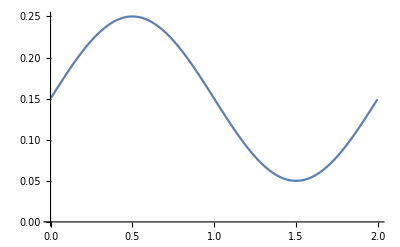

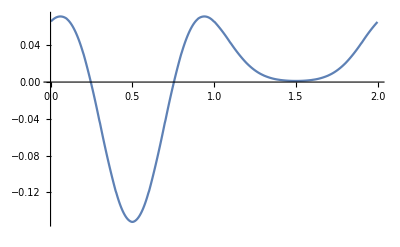

```mathematica
f[x_,t_]:=0.1*Sin[π*(x-t)]+0.15;
g[x_,t_]:=-D[f[ζ,t]^3 D[f[ζ,t],{ζ,3}],ζ]/.{ζ->x}
xLeft = 0.0;
xRight = 2.0;
nCells = 20;
nEqns = 1;
nBasisCpts = 3;
time=0.0;
Δx=(xRight - xLeft)/nCells;
q = L2Project[f, nCells, nBasisCpts, xLeft, xRight, time];
G = L2Project[g,nCells,nBasisCpts,xLeft,xRight,time];
PlotDG[q,xLeft,xRight]
PlotDG[G,xLeft,xRight]
```

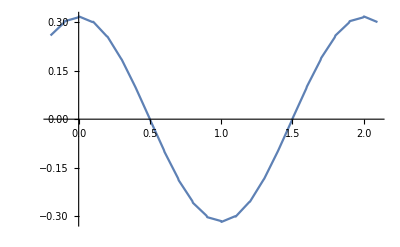

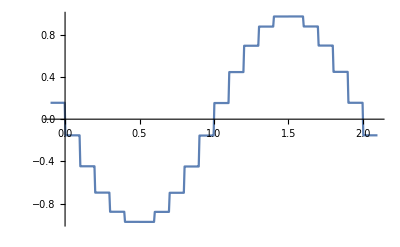

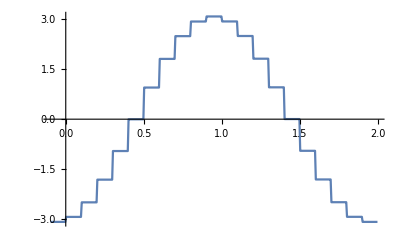

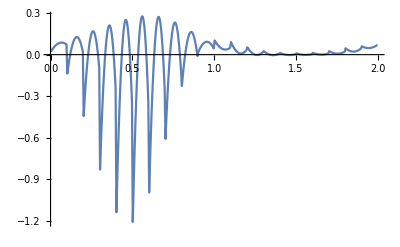

```mathematica
periodicCellRange = Flatten[{nCells-1,nCells,Table[i,{i,1,nCells}],1,2}];
extrapCellRange = Flatten[{1,1,Table[i,{i,1,nCells}],nCells,nCells}];
cellRange = periodicCellRange;
FQ = Table[evaluateQ[q,j,-1],{j,1,nCells}];
r[j_,k_]:=-1/Δx∫_-1^1 evaluateQ[q,cellRange[[j]],ξ]Subscript[ϕ, k]'[ξ]ⅆξ+1/Δx(Subscript[ϕ, k][1]*FQ[[cellRange[[j+1]]]]-Subscript[ϕ, k][-1]*FQ[[cellRange[[j]]]])
R = Table[r[j,k],{j,1,nCells+3},{k,0,Max[nBasisCpts-2,0]}];
PlotDG[R,xLeft-2Δx,xRight+Δx]
FR = Table[evaluateQ[R,j,1],{j,1,nCells+3}];
s[j_,k_]:=-1/Δx∫_-1^1 evaluateQ[R,j+1,ξ]Subscript[ϕ, k]'[ξ]ⅆξ+
1/Δx(Subscript[ϕ, k][1]*FR[[j+1]]-Subscript[ϕ, k][-1]*FR[[j]]);
S = Table[s[j,k],{j,1,nCells+2},{k,0,Max[nBasisCpts-3,0]}];
PlotDG[S,xLeft-Δx,xRight+Δx]
FS = Table[evaluateQ[S,j,-1],{j,1,nCells+2}];
u[j_,k_]:=-1/Δx∫_-1^1 evaluateQ[S,j,ξ]Subscript[ϕ, k]'[ξ]ⅆξ+
1/Δx(Subscript[ϕ, k][1]*FS[[j+1]]-Subscript[ϕ, k][-1]*FS[[j]]);
U = Table[u[j,k],{j,1,nCells+1},{k,0,Max[nBasisCpts-4,0]}];
PlotDG[U,xLeft-Δx,xRight]
FU = Table[evaluateQ[U,j,1],{j,1,nCells+1}];
FQ3 = Table[(1/2(evaluateQ[q,cellRange[[j+1]],1]+evaluateQ[q,cellRange[[j+2]],-1]))^3,{j,1,nCells+1}];
a[j_,k_]:=1/Δx∫_-1^1 evaluateQ[q,j,ξ]^3 evaluateQ[U,j+1,ξ]Subscript[ϕ, k]'[ξ]ⅆξ-1/Δx(Subscript[ϕ, k][1]FU[[j+1]]FQ3[[j+1]]-Subscript[ϕ, k][-1]FU[[j]]FQ3[[j]]);
A = Table[a[j,k],{j,1,nCells},{k,0,nBasisCpts-1}];
PlotDG[A,xLeft,xRight]
```

```mathematica
g[x_,t_]:=-D[f[x,t]^3 D[f[x,t],{x,3}],x]
```

```mathematica
g[x,0.0]//Simplify
```

(0.15+0.1 Sin[π x])^2 (0.974091+1.94818 Cos[π x]^2-1.46114 Sin[π x]-1.94818 Sin[π x]^2)

```mathematica
h[x_]:=-(0.1Sin[π x]+0.15)^3 π^4 0.1Sin[π x] + 3*(0.1Sin[π x]+0.15)^2 π 0.1Cos[π x] π^3 0.1Cos[π x]
```

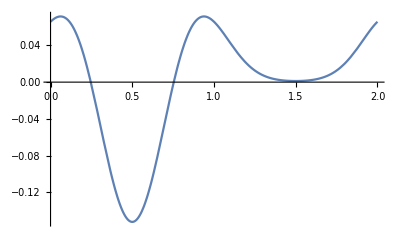

```mathematica
Plot[h[x],{x,0,2}]
```

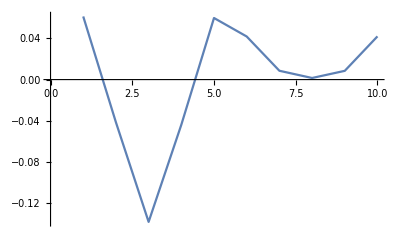

```mathematica
ListPlot[,Joined->True]
```

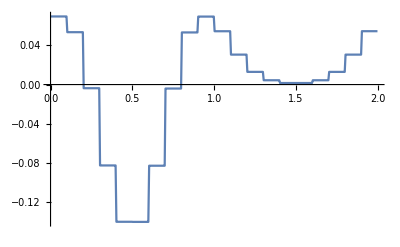

```mathematica
PlotDG[Table[A[[j,k]],{j,1,nCells},{k,1,1}],xLeft,xRight]
```

```mathematica
DSolve[{u'[t]==t^p,u[t0]==u0},u[t],t]
```

{{u[t]→(t^(1+p)-t0^(1+p)+u0+p u0)/(1+p)}}

```mathematica
(t^(1+p)-t0^(1+p)+u0+p u0)/(1+p)//Simplify
```

(t^(1+p)-t0^(1+p)+u0+p u0)/(1+p)

```mathematica
Expand[(t^(1+p)-t0^(1+p)+u0+p u0)/(1+p)]
```

t^(1+p)/(1+p)-t0^(1+p)/(1+p)+u0/(1+p)+(p u0)/(1+p)

```mathematica
u0/(1+p)+(p u0)/(1+p)//Simplify
```

u0